## Generalized Model Analysis of the SH0ES Measurement of H_0. Search for a transition is implemented. For different generalized parameters, the parameter ‘col’ needs to be changed and the table qpar1. The rest may even remain as they are (the range of the final plot may also need to be changed).

## Setting the directory

```mathematica
SetDirectory[NotebookDirectory[]];  
Needs["ErrorBarPlots`"];
Needs["ErrorBarLogPlots`"]
Off[General::"obspkg",General::luc,NIntegrate::"inumr",NIntegrate::ncvb,CompiledFunction::cflist,ListInterpolation::inhr,FindMinimum::lstol,Inverse::luc];
```

## Matrix of Measurements Y- Matrix of Parameters q - Design Matrix L- Error Matrix C

```mathematica
cdata=Import[".\\data\\allc_shoes_ceph_topantheonwt6.0_112221.fits","RawData"];
ydata=Import[".\\data\\ally_shoes_ceph_topantheonwt6.0_112221.fits","RawData"] [[1]]//Normal;
ldata=Import[".\\data\\alll_shoes_ceph_topantheonwt6.0_112221.fits","RawData"]//Normal;
distc=Import[".\\data\\distc.txt","Table"];
```

```mathematica
dist1=distc[[All,1]];
```

```mathematica
dof=3446;
NN=3492;
MM=48;
```

```mathematica
maxdist=60; (* this is the maximum distance considered in do loop in Mpc that distinguishes nearby and distant objects/constraints in Y.  *)
mindist=1; (* this is the minimum distance considered in do loop in Mpc that distinguishes nearby and distant objects/constraints in Y.  *)
step=2; (* this is the distance step considered in do loop  *)

col=47-3; (* this column corresponds to the parameter to be split (e.g. for ZW period luminosity slope we have col=44 *)
qpar1={μ67,μ385,μ354,μ356,μ738,μ294,μ228,μ163,μ193,μ201,μ272,μ354,μ266,μ425,μ244,μ24,μ208,μ344,μ151,μ190,μ293,μ164,μ319,μ198,μ421,μ463,μ280,μ207,μ449,μ303,μ310,μ128,μ468,μ344,μ466,μ605,μ294,ΔμΝ4258,MW,ΔμLMC,μM31,bW,MB,ZWs,ZWl,X,ΔZp,p5ogh0}; (* introduce here the names of the two new parameters that replace the previous parameter *)

Call=cdata[[1]]//Normal; (* Covariance matrix. This does not change since the Y matrix remained the same with no new constraints. *)
InvCall=Inverse[Call];
it=InvCall.Call//Chop;
zerot=it-IdentityMatrix[Length[it]]//Chop;
zerot[[1]];  (* test the inversion of Call due to the mathematica complaints. These are due to the parameter X introduced arbitrarily in the SH0ES data analysis and not shown in https://arxiv.org/pdf/2112.04510.pdf  (Riess21). This leads to Call with a column and raw that are 0 except of the diagonal point which is 10^-9. This raw and column of Call creates the complaints but the end inversion is fine. *)
Y=ydata;
trL=ldata[[1]]//Normal;
L=Transpose[trL]; (* Y = L.qpar . L denotes the original model used by the SH0ES team which will be generalized here. *)
```

## Search for a transition (Ζ_W) - Results - Figure 9

```mathematica
percol1=L[[All,col]]//Normal; (* construct two columns from the  Subscript[Ζ, W] column of L with nearby and distant objects *)
```

Distance=1---------------

H_0=72.4167±1.06235

ZWs=-0.246138±0.0483671

ZWl=-0.0444976±0.109844

σ-distance = 1.68004

Mb=-19.2717±0.0308971

Mw=-5.89214±0.0180708

bw=-0.0143255±0.0149226

χ_min^2 = 3549.8

χ_red^2 = 1.03012

AIC = 3645.8

ΔAIC = -0.954899

BIC = 3941.4

ΔBIC = 5.20333

Distance=3---------------

H_0=72.4167±1.06235

ZWs=-0.246138±0.0483671

ZWl=-0.0444976±0.109844

σ-distance = 1.68004

Mb=-19.2717±0.0308971

Mw=-5.89214±0.0180708

bw=-0.0143255±0.0149226

χ_min^2 = 3549.8

χ_red^2 = 1.03012

AIC = 3645.8

ΔAIC = -0.954899

BIC = 3941.4

ΔBIC = 5.20333

Distance=5---------------

H_0=72.4167±1.06235

ZWs=-0.246138±0.0483671

ZWl=-0.0444976±0.109844

σ-distance = 1.68004

Mb=-19.2717±0.0308971

Mw=-5.89214±0.0180708

bw=-0.0143255±0.0149226

χ_min^2 = 3549.8

χ_red^2 = 1.03012

AIC = 3645.8

ΔAIC = -0.954899

BIC = 3941.4

ΔBIC = 5.20333

Distance=7---------------

H_0=72.507±1.06822

ZWs=-0.240568±0.0482652

ZWl=-0.073147±0.110744

σ-distance = 1.38589

Mb=-19.269±0.0310436

Mw=-5.8923±0.0180737

bw=-0.0142564±0.0149243

χ_min^2 = 3550.75

χ_red^2 = 1.0304

AIC = 3646.75

ΔAIC = -0.0130805

BIC = 3942.34

ΔBIC = 6.14515

Distance=9---------------

H_0=72.4629±1.12668

ZWs=-0.23555±0.0483329

ZWl=-0.0892267±0.123387

σ-distance = 1.1042

Mb=-19.2703±0.0328808

Mw=-5.8961±0.0182015

bw=-0.0137066±0.0149162

χ_min^2 = 3551.53

χ_red^2 = 1.03062

AIC = 3647.53

ΔAIC = 0.769386

BIC = 3943.12

ΔBIC = 6.92762

Distance=11---------------

H_0=72.4629±1.12668

ZWs=-0.23555±0.0483329

ZWl=-0.0892267±0.123387

σ-distance = 1.1042

Mb=-19.2703±0.0328808

Mw=-5.8961±0.0182015

bw=-0.0137066±0.0149162

χ_min^2 = 3551.53

χ_red^2 = 1.03062

AIC = 3647.53

ΔAIC = 0.769386

BIC = 3943.12

ΔBIC = 6.92762

Distance=13---------------

H_0=72.4708±1.12009

ZWs=-0.23552±0.0482353

ZWl=-0.0870773±0.123594

σ-distance = 1.11886

Mb=-19.2701±0.0326712

Mw=-5.8961±0.0181968

bw=-0.0136934±0.0149161

χ_min^2 = 3551.49

χ_red^2 = 1.03061

AIC = 3647.49

ΔAIC = 0.732414

BIC = 3943.09

ΔBIC = 6.89064

Distance=15---------------

H_0=72.4708±1.12009

ZWs=-0.23552±0.0482353

ZWl=-0.0870773±0.123594

σ-distance = 1.11886

Mb=-19.2701±0.0326712

Mw=-5.8961±0.0181968

bw=-0.0136934±0.0149161

χ_min^2 = 3551.49

χ_red^2 = 1.03061

AIC = 3647.49

ΔAIC = 0.732414

BIC = 3943.09

ΔBIC = 6.89064

Distance=17---------------

H_0=72.771±1.11615

ZWs=-0.225277±0.0478441

ZWl=-0.15096±0.126578

σ-distance = 0.549202

Mb=-19.261±0.0323943

Mw=-5.89471±0.0181784

bw=-0.0135631±0.0149155

χ_min^2 = 3552.45

χ_red^2 = 1.03089

AIC = 3648.45

ΔAIC = 1.69191

BIC = 3944.05

ΔBIC = 7.85014

Distance=19---------------

H_0=72.771±1.11615

ZWs=-0.225277±0.0478441

ZWl=-0.15096±0.126578

σ-distance = 0.549202

Mb=-19.261±0.0323943

Mw=-5.89471±0.0181784

bw=-0.0135631±0.0149155

χ_min^2 = 3552.45

χ_red^2 = 1.03089

AIC = 3648.45

ΔAIC = 1.69191

BIC = 3944.05

ΔBIC = 7.85014

Distance=21---------------

H_0=72.4137±1.08981

ZWs=-0.234387±0.0468813

ZWl=-0.0283615±0.138795

σ-distance = 1.40633

Mb=-19.2716±0.0316996

Mw=-5.89595±0.0181321

bw=-0.0135779±0.0149154

χ_min^2 = 3550.7

χ_red^2 = 1.03038

AIC = 3646.7

ΔAIC = -0.057341

BIC = 3942.3

ΔBIC = 6.10089

Distance=23---------------

H_0=71.9534±1.06539

ZWs=-0.247116±0.0465186

ZWl=0.170598±0.14619

σ-distance = 2.72282

Mb=-19.2856±0.0311888

Mw=-5.8977±0.0181152

bw=-0.0133687±0.0149154

χ_min^2 = 3545.

χ_red^2 = 1.02873

AIC = 3641.

ΔAIC = -5.7563

BIC = 3936.6

ΔBIC = 0.401925

Distance=25---------------

H_0=72.2961±1.04154

ZWs=-0.238168±0.0460509

ZWl=0.170893±0.163777

σ-distance = 2.40443

Mb=-19.2753±0.030295

Mw=-5.89648±0.0180927

bw=-0.0133698±0.0149155

χ_min^2 = 3546.7

χ_red^2 = 1.02922

AIC = 3642.7

ΔAIC = -4.05907

BIC = 3938.3

ΔBIC = 2.09916

Distance=27---------------

H_0=72.2975±1.04215

ZWs=-0.237911±0.0460455

ZWl=0.168307±0.164083

σ-distance = 2.38362

Mb=-19.2753±0.0303136

Mw=-5.89644±0.0180924

bw=-0.013377±0.0149155

χ_min^2 = 3546.8

χ_red^2 = 1.02925

AIC = 3642.8

ΔAIC = -3.95439

BIC = 3938.4

ΔBIC = 2.20384

Distance=29---------------

H_0=72.8235±1.04375

ZWs=-0.222155±0.0457856

ZWl=-0.0799302±0.183445

σ-distance = 0.752223

Mb=-19.2595±0.0301354

Mw=-5.89429±0.0180804

bw=-0.0134213±0.0149159

χ_min^2 = 3552.17

χ_red^2 = 1.03081

AIC = 3648.17

ΔAIC = 1.40919

BIC = 3943.76

ΔBIC = 7.56742

Distance=31---------------

H_0=72.714±1.02384

ZWs=-0.225841±0.0455855

ZWl=0.114825±0.21432

σ-distance = 1.55474

Mb=-19.2626±0.0295404

Mw=-5.8948±0.0180708

bw=-0.0133392±0.0149158

χ_min^2 = 3550.26

χ_red^2 = 1.03025

AIC = 3646.26

ΔAIC = -0.502489

BIC = 3941.85

ΔBIC = 5.65574

Distance=33---------------

H_0=72.6605±1.01345

ZWs=-0.227707±0.0454274

ZWl=0.428544±0.262344

σ-distance = 2.46481

Mb=-19.2642±0.0292484

Mw=-5.89509±0.0180638

bw=-0.0127559±0.0149185

χ_min^2 = 3546.53

χ_red^2 = 1.02917

AIC = 3642.53

ΔAIC = -4.23221

BIC = 3938.12

ΔBIC = 1.92602

Distance=35---------------

H_0=72.8483±1.00942

ZWs=-0.223685±0.0453558

ZWl=0.386051±0.313329

σ-distance = 1.92592

Mb=-19.2587±0.029051

Mw=-5.89454±0.0180604

bw=-0.0127738±0.0149203

χ_min^2 = 3548.98

χ_red^2 = 1.02988

AIC = 3644.98

ΔAIC = -1.77787

BIC = 3940.58

ΔBIC = 4.38036

Distance=37---------------

H_0=72.8787±1.00982

ZWs=-0.222002±0.0453284

ZWl=0.33169±0.336648

σ-distance = 1.63001

Mb=-19.2578±0.0290496

Mw=-5.89429±0.018059

bw=-0.0129748±0.0149191

χ_min^2 = 3550.06

χ_red^2 = 1.0302

AIC = 3646.06

ΔAIC = -0.701132

BIC = 3941.65

ΔBIC = 5.4571

Distance=39---------------

H_0=72.9218±1.00752

ZWs=-0.222574±0.04532

ZWl=0.465923±0.365018

σ-distance = 1.87183

Mb=-19.2565±0.0289628

Mw=-5.89438±0.0180586

bw=-0.0129021±0.014919

χ_min^2 = 3549.21

χ_red^2 = 1.02995

AIC = 3645.21

ΔAIC = -1.5506

BIC = 3940.8

ΔBIC = 4.60763

Distance=41---------------

H_0=72.9218±1.00752

ZWs=-0.222574±0.04532

ZWl=0.465923±0.365018

σ-distance = 1.87183

Mb=-19.2565±0.0289628

Mw=-5.89438±0.0180586

bw=-0.0129021±0.014919

χ_min^2 = 3549.21

χ_red^2 = 1.02995

AIC = 3645.21

ΔAIC = -1.5506

BIC = 3940.8

ΔBIC = 4.60763

Distance=43---------------

H_0=72.8604±1.00808

ZWs=-0.222707±0.0452951

ZWl=0.629662±0.389821

σ-distance = 2.17195

Mb=-19.2584±0.0290078

Mw=-5.89441±0.0180574

bw=-0.0127709±0.0149193

χ_min^2 = 3547.98

χ_red^2 = 1.02959

AIC = 3643.98

ΔAIC = -2.77689

BIC = 3939.58

ΔBIC = 3.38134

Distance=45---------------

H_0=72.8335±1.00906

ZWs=-0.222088±0.0452824

ZWl=0.633692±0.402205

σ-distance = 2.11436

Mb=-19.2592±0.0290488

Mw=-5.89432±0.0180568

bw=-0.0128126±0.0149191

χ_min^2 = 3548.23

χ_red^2 = 1.02967

AIC = 3644.23

ΔAIC = -2.52634

BIC = 3939.83

ΔBIC = 3.63189

Distance=47---------------

H_0=72.9813±1.00698

ZWs=-0.217486±0.0452117

ZWl=2.58781±1.68599

σ-distance = 1.66329

Mb=-19.2547±0.028918

Mw=-5.89364±0.018053

bw=-0.0135977±0.0149154

χ_min^2 = 3549.99

χ_red^2 = 1.03018

AIC = 3645.99

ΔAIC = -0.768746

BIC = 3941.59

ΔBIC = 5.38948

Distance=49---------------

H_0=72.9813±1.00698

ZWs=-0.217486±0.0452117

ZWl=2.58781±1.68599

σ-distance = 1.66329

Mb=-19.2547±0.028918

Mw=-5.89364±0.018053

bw=-0.0135977±0.0149154

χ_min^2 = 3549.99

χ_red^2 = 1.03018

AIC = 3645.99

ΔAIC = -0.768746

BIC = 3941.59

ΔBIC = 5.38948

Distance=51---------------

H_0=72.9813±1.00698

ZWs=-0.217486±0.0452117

ZWl=2.58781±1.68599

σ-distance = 1.66329

Mb=-19.2547±0.028918

Mw=-5.89364±0.018053

bw=-0.0135977±0.0149154

χ_min^2 = 3549.99

χ_red^2 = 1.03018

AIC = 3645.99

ΔAIC = -0.768746

BIC = 3941.59

ΔBIC = 5.38948

Distance=53---------------

H_0=72.9813±1.00698

ZWs=-0.217486±0.0452117

ZWl=2.58781±1.68599

σ-distance = 1.66329

Mb=-19.2547±0.028918

Mw=-5.89364±0.018053

bw=-0.0135977±0.0149154

χ_min^2 = 3549.99

χ_red^2 = 1.03018

AIC = 3645.99

ΔAIC = -0.768746

BIC = 3941.59

ΔBIC = 5.38948

Distance=55---------------

H_0=72.9813±1.00698

ZWs=-0.217486±0.0452117

ZWl=2.58781±1.68599

σ-distance = 1.66329

Mb=-19.2547±0.028918

Mw=-5.89364±0.018053

bw=-0.0135977±0.0149154

χ_min^2 = 3549.99

χ_red^2 = 1.03018

AIC = 3645.99

ΔAIC = -0.768746

BIC = 3941.59

ΔBIC = 5.38948

Distance=57---------------

H_0=72.9813±1.00698

ZWs=-0.217486±0.0452117

ZWl=2.58781±1.68599

σ-distance = 1.66329

Mb=-19.2547±0.028918

Mw=-5.89364±0.018053

bw=-0.0135977±0.0149154

χ_min^2 = 3549.99

χ_red^2 = 1.03018

AIC = 3645.99

ΔAIC = -0.768746

BIC = 3941.59

ΔBIC = 5.38948

Distance=59---------------

H_0=72.9813±1.00698

ZWs=-0.217486±0.0452117

ZWl=2.58781±1.68599

σ-distance = 1.66329

Mb=-19.2547±0.028918

Mw=-5.89364±0.018053

bw=-0.0135977±0.0149154

χ_min^2 = 3549.99

χ_red^2 = 1.03018

AIC = 3645.99

ΔAIC = -0.768746

BIC = 3941.59

ΔBIC = 5.38948

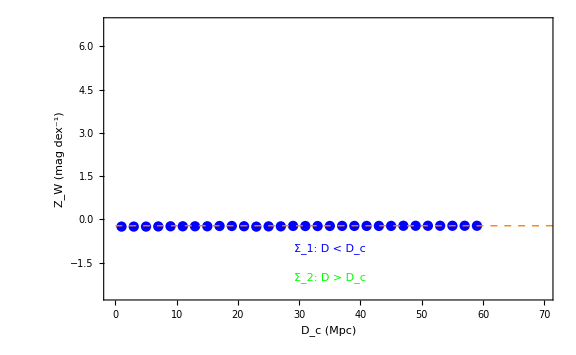
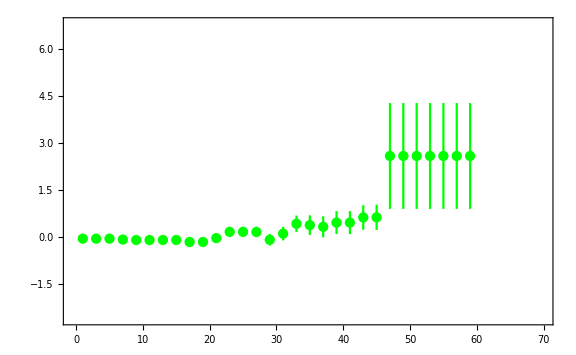
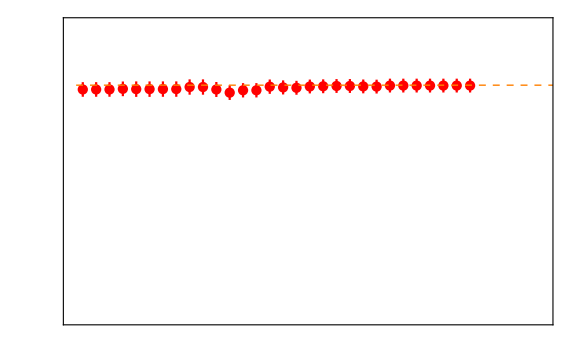

```mathematica
plh0dat={};
plparsdat={};
plparldat={};
plsdist={};
plchi2min={};
plchi2red={};
plaic={};
pldaic={};
plbic={};
pldbic={};
Do[
percol1s=percol1;
percol1l=percol1;
Do[
If[dist1[[i]]≥ dcrit,percol1s[[i]]=0]; (* in the nearby Subscript[Ζ, W,s] column put 0 in the distant elements ie those that are beyond dcrit *)
If[0<=dist1[[i]]< dcrit,percol1l[[i]]=0] (* in the distant Subscript[Ζ, W,l] column put 0 in the nearby elements ie those that are closer than dcrit. Elements with negative distance are ignored. *)
,{i,1,Length[dist1]}];
trL1=Drop[trL,{col}] ;(* Remove the ZW column of L to replace it with two other columns for the nearby and distant parameters (Subscript[Ζ, W,s] and Subscript[Ζ, W,l]) *)
trL2=Insert[Insert[trL1,percol1s,col],percol1l,col+1] ;(* Replace with the new columns *)
Lnew=Transpose[trL2]; (* this is the model matrix Lnew for the new model with one new parameter *)
trLnew=trL2 ;(* The system is Y=L qpar. qpar has single column with 47 entries. Entry 45 is useless and does not appear anywhere but we keep it for completeness as it has been included in the fits data but it is not mentioned in Riess 21. *);
sigma=Inverse[trLnew.InvCall.Lnew];
qbf=sigma.(trLnew.InvCall.Y) ;(* These are the best fit parameter values. These formulas are proven in https://people.duke.edu/~hpgavin/SystemID/CourseNotes/linear-least-squres.pdf eq. 11 *);
(* the best fit papameter values with 1 sigma errors for H0 and for the two new parameters *)
h0=10^(qbf[[48]]/5) (* We obtain the correct value of h0 since qbf[[47]]= 5 log Subscript[H, 0] *);
dqbf48=Sqrt[sigma[[48,48]]];
dh0=Log[10] h0 dqbf48/5 ;
vec=Y-Lnew.qbf;
chi2min=vec.InvCall.vec;
Print["Distance=",dcrit,"---------------"];
Print["H_0=",h0,"±",dh0];
dpars=Sqrt[sigma[[col,col]]];
dparl=Sqrt[sigma[[col+1,col+1]]];
pars=ToString[qpar1[[col]]];
parl=ToString[qpar1[[col+1]]];
sdist=Abs[(qbf[[col]] -qbf[[col+1]])]/(dpars ^2+dparl ^2)^0.5(* We obtain the σ-distance *);
Print[pars,"=",qbf[[col]],"±",dpars];
Print[parl,"=",qbf[[col+1]],"±",dparl];
Print["σ-distance = ",sdist];
Print["Mb","=",qbf[[43]],"±",Sqrt[sigma[[43,43]]]];
Print["Mw","=",qbf[[39]],"±",Sqrt[sigma[[39,39]]]];
Print["bw","=",qbf[[42]],"±",Sqrt[sigma[[42,42]]]];
Print["χ_min^2 = ",chi2min];
Print["χ_red^2 = ",chi2min/dof];
Print["AIC = ",chi2min+2*MM];
Print["ΔAIC = ",chi2min+2*MM-3646.7593303](* this is the AIC obtained from the zero order model of SH0ES (see Baseline1 file)*);
Print["BIC = ",chi2min+MM*Log[NN]];
Print["ΔBIC = ",chi2min+MM*Log[NN]-3936.1961364](* this is the BIC obtained from the zero order model of SH0ES (see Baseline1 file)*);
AppendTo[plh0dat,{dcrit,h0,dh0}];
AppendTo[plparsdat,{dcrit,qbf[[col]],dpars}];
AppendTo[plparldat,{dcrit,qbf[[col+1]],dparl}];
AppendTo[plsdist,{dcrit,sdist}];
AppendTo[plchi2min,{dcrit,chi2min}];
AppendTo[plchi2red,{dcrit,chi2min/dof}];
AppendTo[plaic,{dcrit,chi2min+2*MM}];
AppendTo[pldaic,{dcrit,chi2min+2*MM-3646.7593303}](* this is the AIC obtained from the zero order model of SH0ES (see Baseline1 file)*);
AppendTo[plbic,{dcrit,chi2min+MM*Log[NN]}];
AppendTo[pldbic,{dcrit,chi2min+MM*Log[NN]-3936.1961364}](* this is the BIC obtained from the zero order model of SH0ES (see Baseline1 file)*);
chi2min0=3552.76 (* this is the Subscript[χ, min]^2 obtained from the zero order model of SH0ES (see Baseline1 file)*);
deltachi2min=chi2min-chi2min0  (* this is the improvement of chi2min obtained by the introduction of the new parameter *),{dcrit,mindist,maxdist,step}]
data1=plparsdat;
data2=plparldat;
data3=plh0dat;
plot1=ErrorListPlot[data1,PlotRange->{{-0.5,70},{-2.6,6.8}},Axes->False,PlotStyle->Blue,ImagePadding->70,Frame->{{True,False},{True,True}},FrameStyle->Directive[{{Blue,Automatic},{Blue,Blue}},Thick],FrameLabel->{"D_c (Mpc)","Ζ_W (mag dex^-1)"},BaseStyle->{Large,FontFamily->"Times",18},Epilog->{{Dashing[{Small,Small}],Thickness[Medium],Orange,Line[{{0,-0.217},{80,-0.217}}]},{Blue,Inset["Σ_1: D < D_c",{35,-1}]},{Green,Inset["Σ_2: D > D_c",{35,-2}]}}];
plot2=ErrorListPlot[data2,PlotRange->{{-0.5,70},{-2.6,6.8}},Axes->False,PlotStyle->Green,ImagePadding->70,Frame->{{True,False},{True,True}},FrameStyle->Directive[{{Blue,Automatic},{Blue,Blue}},Thick],BaseStyle->{Large,FontFamily->"Times",18}];
plot3=ErrorListPlot[data3,PlotRange->{{-0.5,70},{39,82}},Axes->False,PlotStyle->Red,ImagePadding->70,Axes->False,Frame->{{False,True},{False,False}},FrameTicks->{{None,All},{None,None}},FrameStyle->Directive[{{Automatic,Red},{Automatic,Red}},Thick],FrameLabel->{{None,"H_0 (km sec^-1 Mpc^-1)"},{None,None}},BaseStyle->{Large,FontFamily->"Times",18},Epilog->{Dashing[{Small,Small}],Thickness[Medium],Orange,Line[{{0,73.04},{80,73.04}}]}];
figzw=Overlay[Show[#,ImageSize->Large]&/@{plot1,plot2,plot3}]
```

```mathematica
Export[NotebookDirectory[]<>"figzw.pdf",figzw,ImageResolution->1000];
```

## Figures 10, 11

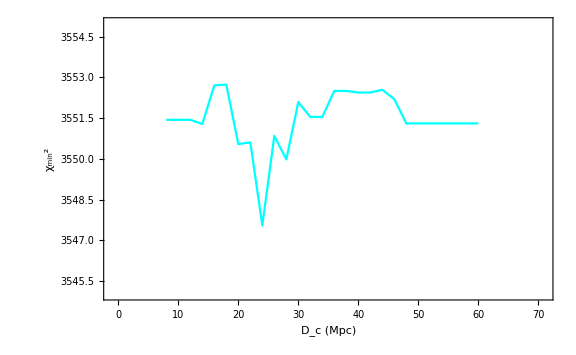
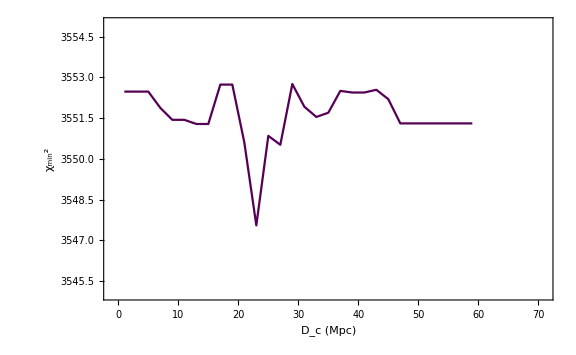
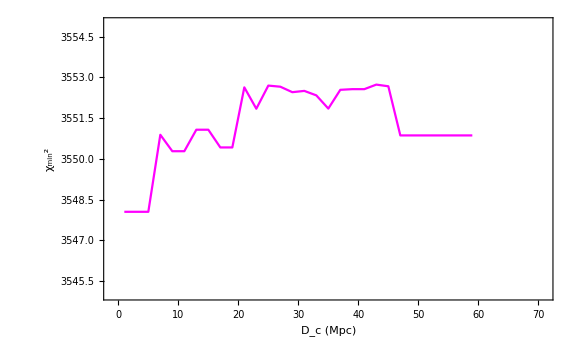
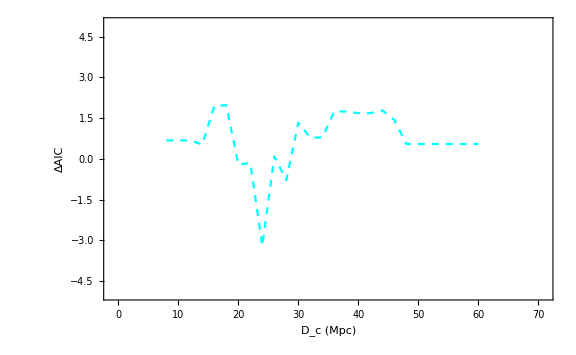
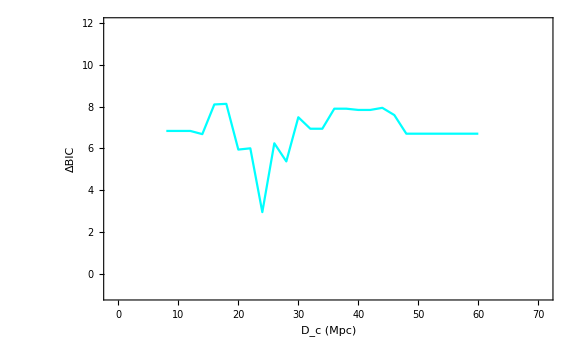
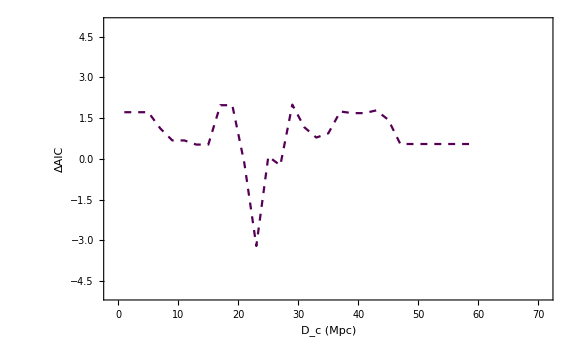
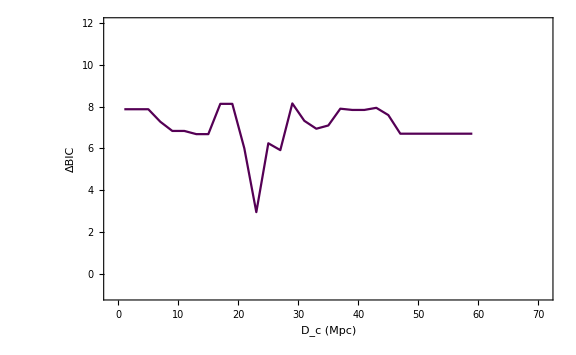
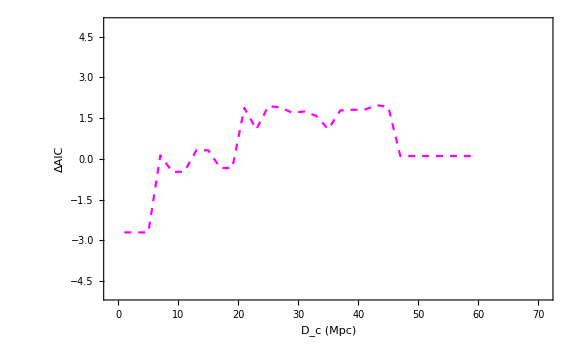
```mathematica
(* We obtain the σ-distance plot for the transition model Subscript[Z, W]*)
figsdzw=ListPlot[plsdist,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","σ-distance (Z_W)"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{-0.5,4}},Axes->False,PlotStyle->{Darker[Green]},ImageSize->Large, FrameStyle -> Directive[Black, Thick]];
(* We obtain the Subscript[χ, min]^2 plot for the transition model Subscript[Z, W]*)
figchizw=ListPlot[plchi2min,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","χ_min^2"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{3542,3555}},Axes->False,PlotStyle->{Darker[Green]},ImageSize->Large, FrameStyle -> Directive[Black, Thick]];

figchimb=-Graphics-(* this is the Subscript[χ, min]^2 plot obtained from the transition model Subscript[M, B]*);

figchimw=-Graphics-(* this is the Subscript[χ, min]^2 plot obtained from the transition model Subscript[M, W]*);
figchibw=-Graphics-(* this is the Subscript[χ, min]^2 plot obtained from the transition model Subscript[b, W]*);
(* We obtain the Subscript[χ, min]^2 plot for the four transition models *)
figchiall=Show[figchizw,figchibw,figchimw,figchimb,Graphics[{Inset[" - Transition: Z_W",{55,3560.5},BaseStyle->{Italic,Bold,Darker[Green],FontFamily->"Times",12}]}],Graphics[{Inset[" - Transition: b_W",{55,3559},BaseStyle->{Italic,Bold,Magenta,FontFamily->"Times",12}]}],Graphics[{Inset[" - Transition: M_H^W",{55,3557.5},BaseStyle->{Italic,Bold,Purple,FontFamily->"Times",12}]}],Graphics[{Inset[" - Transition: M_B",{55,3556},BaseStyle->{Italic,Bold,Cyan,FontFamily->"Times",12}]}],Graphics[{Inset[" - No Transition",{55,3554.5},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",12}]}],Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","χ_min^2"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{3542,3563}},Axes->False,PlotStyle->{Darker[Green]},ImageSize->Large,Epilog->{Dashed,Red,Line[{{-1,3552.76},{80,3552.76}}]}, FrameStyle -> Directive[Black, Thick]]
Export[NotebookDirectory[]<>"figchiall.pdf",figchiall,ImageResolution->1000];
(* We obtain the Subscript[χ, red]^2 plot for the transition model Subscript[Z, W]*)
figchiredzw=ListPlot[plchi2red,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","χ_red^2"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{1.0285,1.032}},Axes->False,PlotStyle->{Darker[Green]},ImageSize->Large, FrameStyle -> Directive[Black, Thick]];
(* We obtain the AIC plot for the transition model Subscript[Z, W]*)
figaiczw=ListPlot[plaic,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","AIC"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{3632,3651}},Axes->False,PlotStyle->{Darker[Green]},ImageSize->Large, FrameStyle -> Directive[Black, Thick]];
(* We obtain the ΔAIC plot for the transition model Subscript[Z, W]*)
figdaiczw=ListPlot[pldaic,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","ΔAIC"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{-7,5}},Axes->False,PlotStyle->{Dashed,Darker[Green]},ImageSize->Large, FrameStyle -> Directive[Black, Thick]];
(* We obtain the BIC plot for the transition model Subscript[Z, W]*)
figbiczw=ListPlot[plbic,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","BIC"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{3930,3951}},Axes->False,PlotStyle->{Darker[Green]},ImageSize->Large, FrameStyle -> Directive[Black, Thick]];
(* We obtain the ΔBIC plot for the transition model Subscript[Z, W]*)
figdbiczw=ListPlot[pldbic,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","ΔBIC"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{-1,12}},Axes->False,PlotStyle->{Darker[Green]},ImageSize->Large, FrameStyle -> Directive[Black, Thick]];
figdaicmb=-Graphics-(* this is the ΔAIC plot obtained from the transition model Subscript[M, B]*);
figdbicmb=-Graphics-(* this is the ΔBIC plot obtained from the transition model Subscript[M, B]*);
figdaicmw=-Graphics-(* this is the ΔAIC plot obtained from the transition model Subscript[M, W]*);
figdbicmw=-Graphics-(* this is the ΔBIC plot obtained from the transition model Subscript[M, W]*);
figdaicbw=-Graphics-(* this is the ΔAIC plot obtained from the transition model Subscript[b, W]*);
figdbicbw=-Graphics-(* this is the ΔBIC plot obtained from the transition model Subscript[b, W]*);
(* We obtain the ΔAIC/ΔBIC plot for the four transition models *)
figdaicdbicall=Show[figdaiczw,figdbiczw,figdaicmb,figdbicmb,figdaicmw,figdbicmw,figdaicbw,figdbicbw,Graphics[{Inset[" - Transition: Z_W",{55,16},BaseStyle->{Italic,Bold,Darker[Green],FontFamily->"Times",12}]}],Graphics[{Inset[" - Transition: b_W",{55,14.5},BaseStyle->{Italic,Bold,Magenta,FontFamily->"Times",12}]}],Graphics[{Inset[" - Transition: M_H^W",{55.1,13},BaseStyle->{Italic,Bold,Purple,FontFamily->"Times",12}]}],Graphics[{Inset[" - Transition: M_B",{55,11.5},BaseStyle->{Italic,Bold,Cyan,FontFamily->"Times",12}]}],Graphics[{Inset[" - No Transition ",{55,10},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",12}]}],Graphics[{Inset[" — ΔBIC",{10,15},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12}]}],Graphics[{Inset[" - - ΔAIC",{10,13},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12}]}],Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","ΔAIC/ΔBIC"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{-8,18}},Axes->False,PlotStyle->{Darker[Green]},ImageSize->Large,Epilog->{Dashing[0.02],Red,Line[{{-1,0},{80,0}}]}, FrameStyle -> Directive[Black, Thick]]

Export[NotebookDirectory[]<>"figdaicdbicall.pdf",figdaicdbicall,ImageResolution->1000];
```